# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport["~/Desktop/ALL_runs_MH_mathematica.txt"];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport["~/Desktop/CDF_runs_mathematica.txt"];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(1/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2 π(Dα/μ)^(1/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

General::ivar: 2 is not a valid variable.

Series[1/(π (1/2+2 √(Dα/μ) μ ρ)),{2,1,1}]

```mathematica
exphom[x_,coal_,μ_,Dα_:250^2/2]:=Exp[-√(μ/Dα)x]/(1+4√(μ Dα)/coal)
```

```mathematica
xlist=10^Range[-6,3.5,.25];
```

```mathematica
xlist
```

{1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[Cos[k x]/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlist⟦;;-2⟧}]];
```

```mathematica
xmaxes=AssociationThread[αlist,{6400,3200,1600,400,200,100,30,20,8}];
```

# Plots

## α=0.5

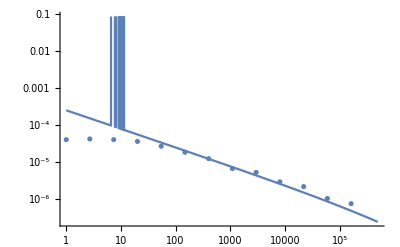

```mathematica
Module[{α=0.5, coal=0.01, μ = 0.001, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coal/2 fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->All]]
```

```mathematica
(* note that coal here is 1/rho, i.e. 1 over the population density*)
```

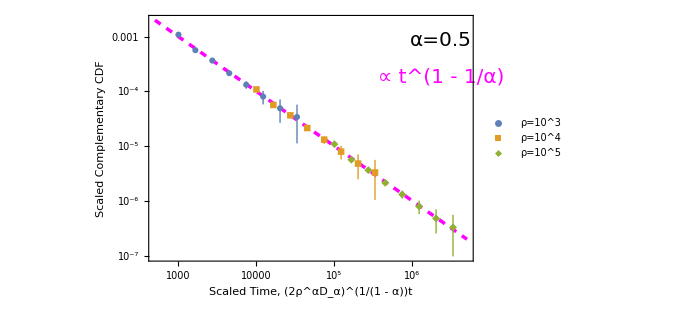

```mathematica
Module[{α=0.5, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->maxcdf*#coal/.001 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->3.141*((1/α -1)/(Gamma[1/α +1]))*#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfHigh|>&];
dummy= dummy[Select[#T < 50 &]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[x^(1-1/α),{x,500,5000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
maxcdf
```

0.000693185

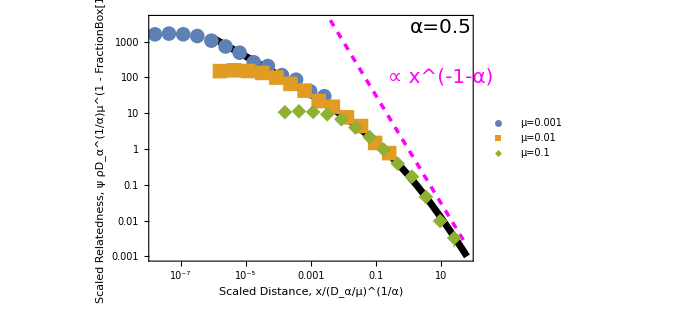

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.9,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

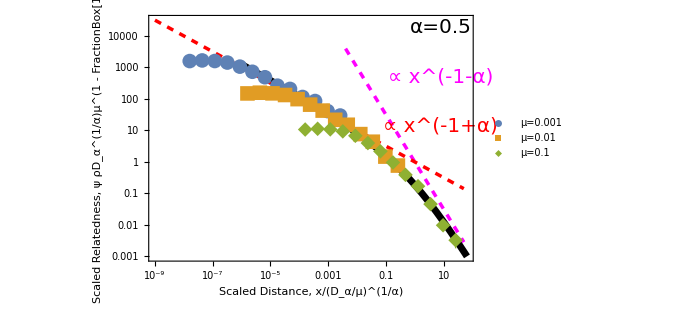

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.000000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.9,.55}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.9,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

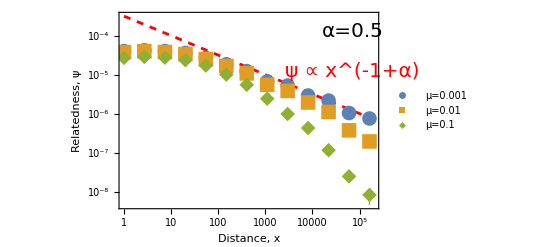

```mathematica
Module[{α=0.5,D = (250)^(2), coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*coal*D))*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.9}]],Text[Style[" ψ ∝ x^(-1+α) ",Red,20],Scaled[{.9,.7}]]},goodlabel["Distance, x","Relatedness, ψ",20],FrameStyle->Directive[20,Black],
PlotRange->All,Axes->False]]
```

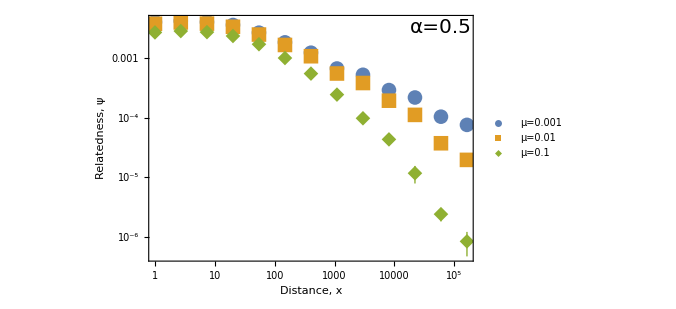

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Relatedness, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False ]]
```

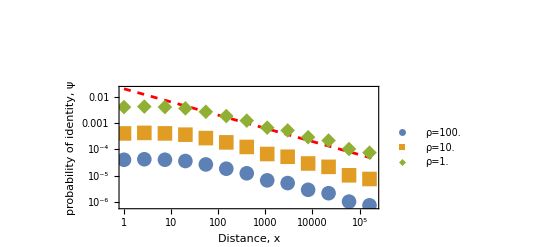

```mathematica
Module[{α=0.5,μ =0.001, plotpoints,coalvals=coallist⟦;;3⟧,yscale=80000},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{coal,coalvals}];
Show[LogLogPlot[.02*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@(coalvals^-1),{.2,.3}]],Epilog->{Text[Style["α=0.5",20],{5,7}],Text[Style["x^(-1-α)",Magenta,20],{0,4}]},goodlabel["Distance, x","probability of identity, ψ",20],FrameStyle->Directive[20,Black],
PlotRange->All,Axes->False]]
```

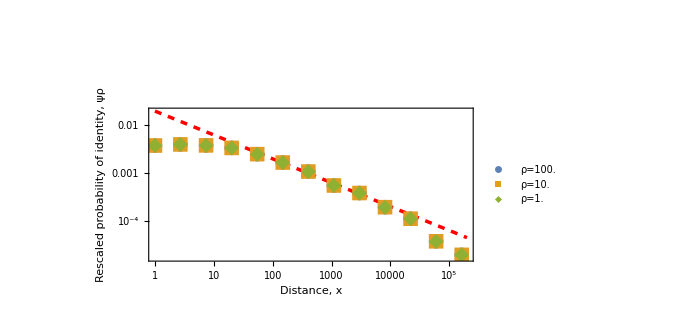

```mathematica
Module[{α=0.5,μ =0.01, plotpoints,coalvals=coallist⟦;;3⟧,yscale=80000},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]/(#coal)}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{coal,coalvals}];
Show[LogLogPlot[.02*x^(-1+α),{x,1,200000},PlotStyle->{Red,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@(coalvals^-1),{.2,.3}]],Epilog->{Text[Style["α=0.5",20],{5,7}],Text[Style["x^(-1-α)",Magenta,20],{0,4}]},goodlabel["Distance, x","Rescaled probability of identity, ψρ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=.75

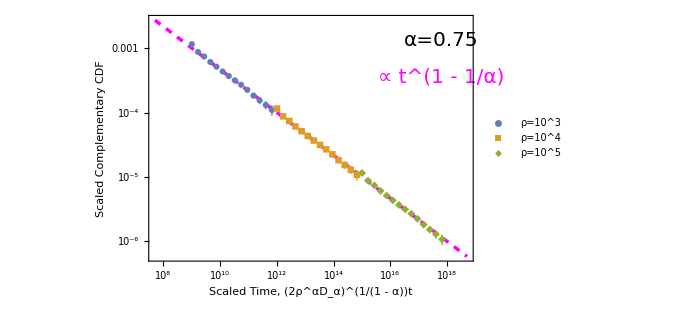

```mathematica
Module[{α=0.75, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->maxcdf*#coal/.001 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->3.141*((1/α -1)/(Gamma[1/α +1]))*#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->3.141*((1/α -1)/(Gamma[1/α +1]))*#dcdfHigh|>&];
dummy= dummy[Select[#T < 1000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[x^(1-1/α),{x,50000000,5000000000000000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.75",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

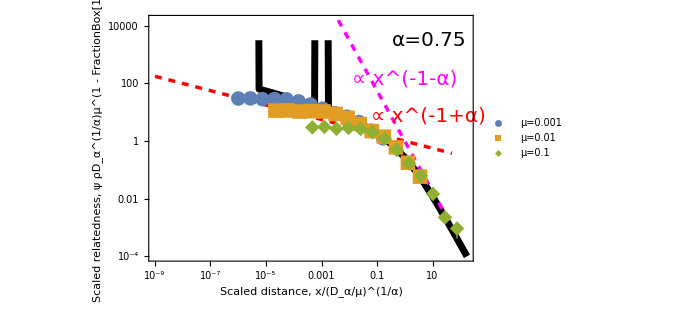

```mathematica
Module[{α=0.75,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-6,20},{10^-4,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.000000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.75",20],{2,8}],Text[Style["∝ x^(-1+α)",Red,20],{2,2}], Text[Style["∝ x^(-1-α)",Magenta,20],{0,5}]},goodlabel["Scaled distance, x/(D_α/μ)^(1/α)","Scaled relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

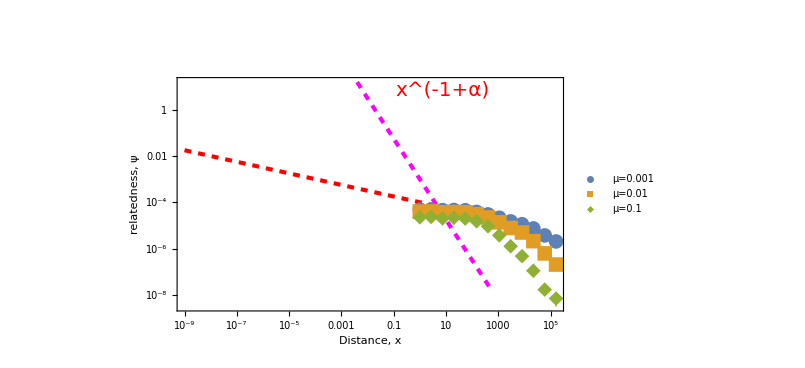

```mathematica
Module[{α=0.75,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[.001*x^(-1-α),{x,.004,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[.0001*x^(-1+α),{x,.000000001,500},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.75",20],{2,8}],Text[Style["x^(-1+α)",Red,20],{2,2}], Text[Style["x^(-1-α)",Magenta,20],{0,5}]},goodlabel["Distance, x","relatedness, ψ ",20],FrameStyle->Directive[20,Black], 
PlotRange->All,Axes->False]]
```

## α=1

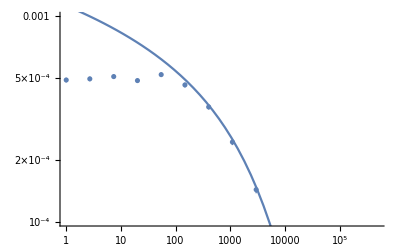

```mathematica
Module[{α=1.0, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[.05fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->{All,{-4,-3}Log[10]}]]
```

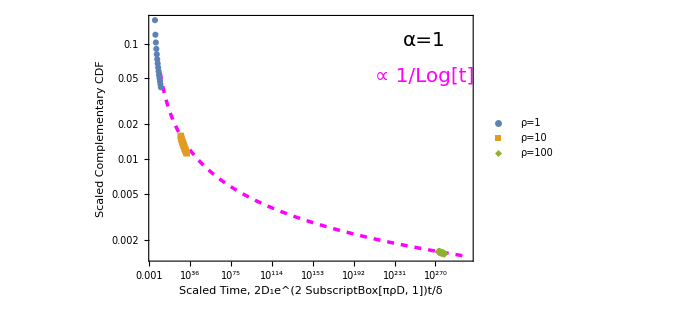

```mathematica
Module[{α=1.00, coal=1, plotcdf, c =1, D =1},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(D*Exp[2*Pi/#coal])*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#coal*#compcdf/(2*Pi*D)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#coal*#dcdfLow/(2*Pi*D)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#coal*#dcdfHigh/(2*Pi*D)|>&];
dummy= dummy[Select[#T < 500000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{ 1, .1, .01}}];



Show[LogLogPlot[1/Log[x],{x,10^1,10^300},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{ "1", "10", "100"},Scaled[{.2,.2}]]],Epilog->{Text[Style["α=1",20],Scaled[{.85,.9}]],Text[Style["∝ 1/Log[t]",Magenta,20],Scaled[{.85,.75}]], ImageSize->500 },goodlabel["Scaled Time, 2D_1e^(2 SubscriptBox[πρD, 1])t/δ","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
dummy
```

Dataset[<>]

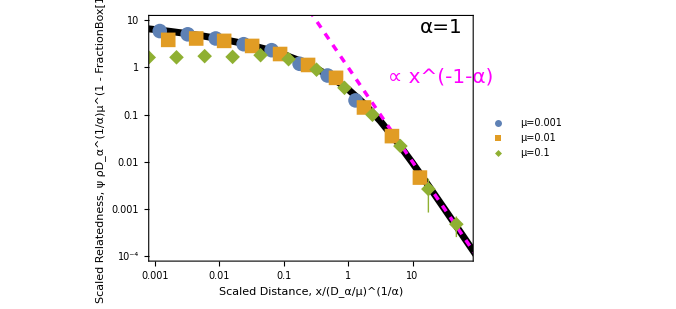

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦;;3⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

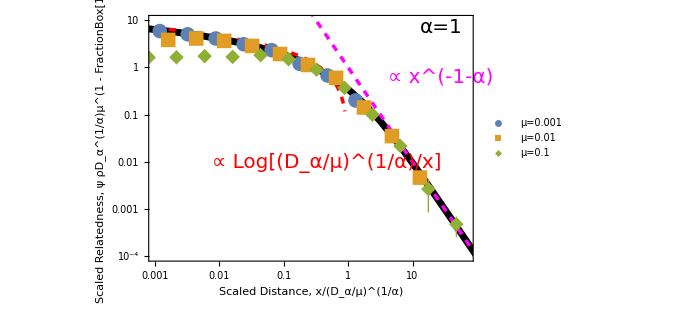

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦;;3⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}], LogLogPlot[Log[1/x],{x,.001,5000},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ Log[(D_α/μ)^(1/α)/x]",Red,20],Scaled[{0.55,.4}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α = 1.25

```mathematica
250^1.25/2
```

497.044

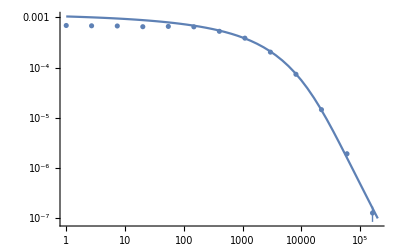

```mathematica
Module[{α=1.25, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],PlotRange->All]]
```

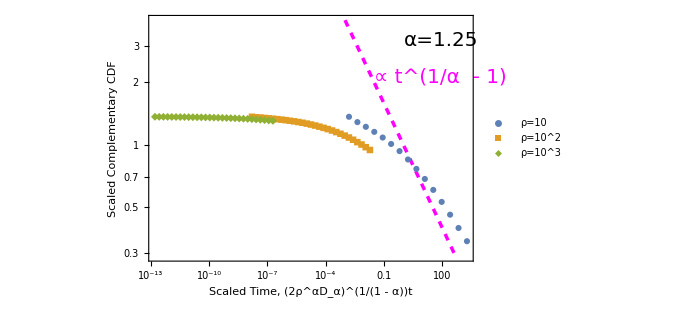

```mathematica
Module[{α=1.25, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
dummy
```

Dataset[<>]

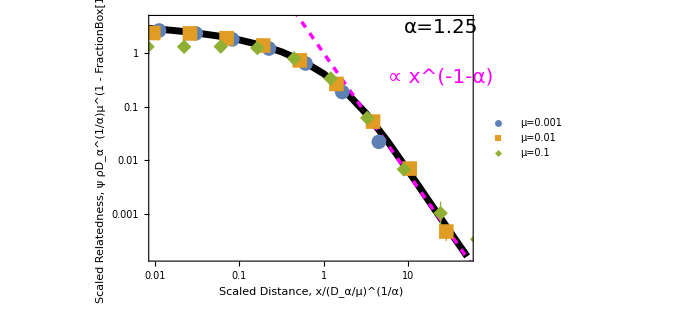

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

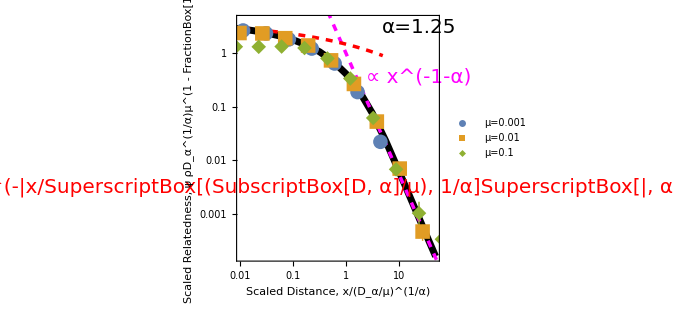

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[4*Exp[-x^(α-1)],{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.45

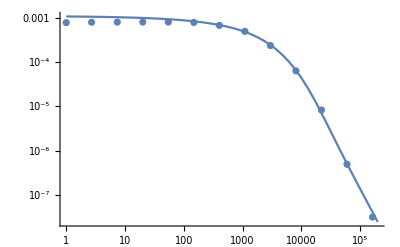

```mathematica
Module[{α=1.45, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],
PlotRange->All]]
```

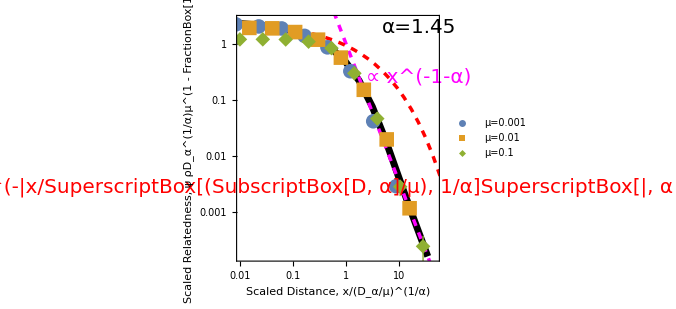

```mathematica
Module[{α=1.45,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[2.5*Exp[-x^(α-1)],{x,.001,5000},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

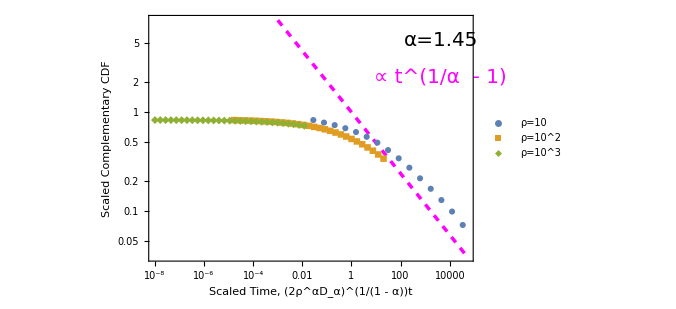

```mathematica
Module[{α=1.45, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=1.65

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (0.31831 Cos[1.00024 k])/(0.01+4524.5 (0.+k)^1.65) over {0,∞}. DoubleExponentialOscillatory obtained 0.0238148 and 2.01953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {283.95}. NIntegrate obtained 0.0238146 and 5.71187×10^-7 for the integral and error estimates.

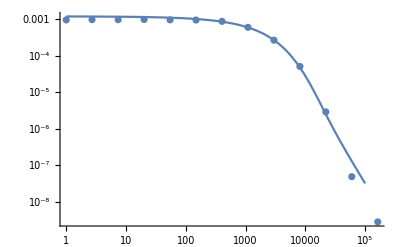

```mathematica
Module[{α=1.65, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 10^5}],
PlotRange->All]]
```

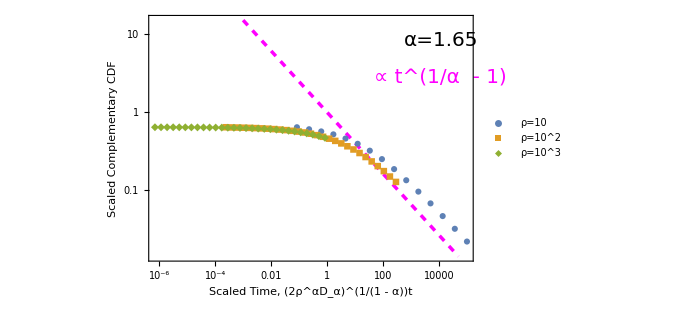

```mathematica
Module[{α=1.65, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

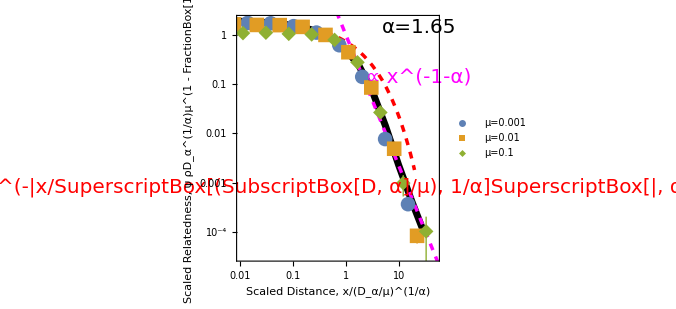

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}], LogLogPlot[2*Exp[-x^(α-1)],{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogLogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.55,.3}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.9,0.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

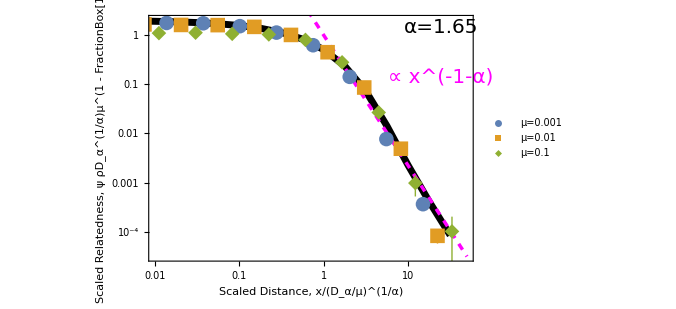

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤1000*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}],
LogLogPlot[x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.9,0.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

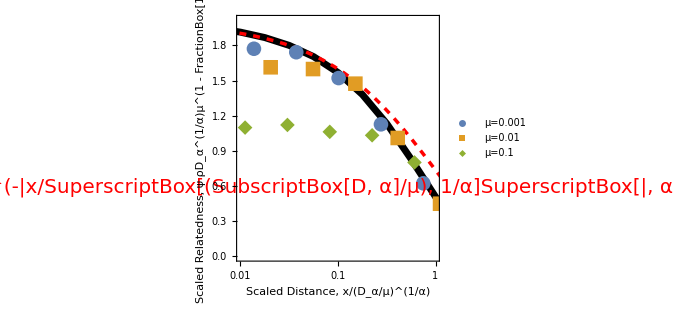

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLinearPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-6,All}}], LogLinearPlot[2*Exp[-x^(α-1)],{x,.0001,10},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLinearPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],{3,1}], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],{0.6,0.8}]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Relatedness, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.85

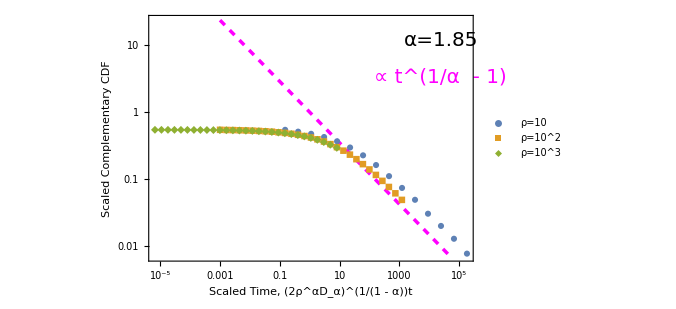

```mathematica
Module[{α=1.85, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(α*Sin[Pi/α])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(α*Sin[Pi/α])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(α*Sin[Pi/α])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^αD_α)^(1/(1 - α))t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

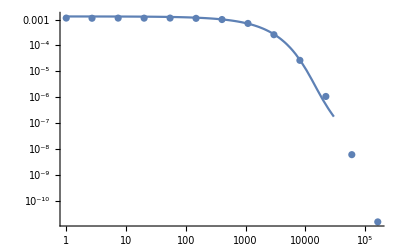

```mathematica
Module[{α=1.85, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 3 10^4}],
PlotRange->All]]
```

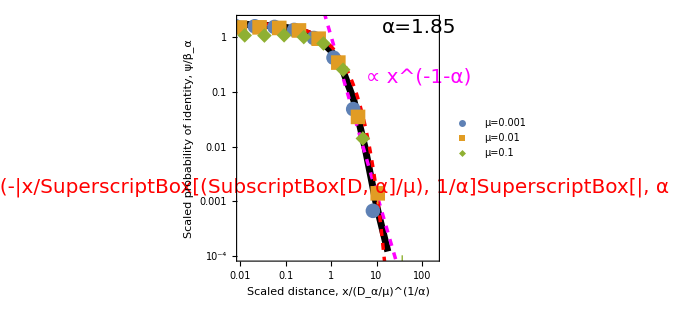

```mathematica
Module[{α=1.85,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,200},{10^-4,2}}],
LogLogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[1.8*Exp[-x^(α-1)],{x,.001,500000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.48,.3}]]},goodlabel["Scaled distance, x/(D_α/μ)^(1/α)","Scaled probability of identity, ψ/β_α",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=2.05 (F distribution)

Null

```mathematica
df =0.5Module[{α=2.05},Moment[FRatioDistribution[2α,2α],2]]
```

59.5476

```mathematica
250^2.05/2
```

41185.8

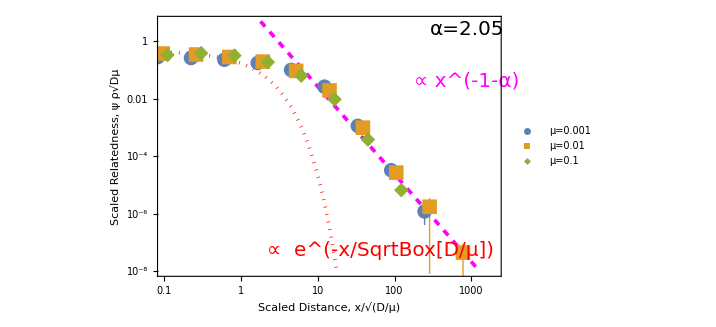

```mathematica
Module[{α=2.05,coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/(√(df/#mu)),Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,2,df]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[
LogLogPlot[{30*x^(-1-α), 2*(1*.1*Sqrt[125/.1])/(1+1*4*Sqrt[125*.1])*Exp[-x]},{x,.01,2000},PlotStyle->{{Magenta,Dashed,Thickness[.005]},{Red,Dotted,Thickness[.005]}},PlotRange->{{.1,2000},{10^-8,5}}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.9,0.75}]],
Text[Style["  ∝  e^(-x/SqrtBox[D/μ])",Red,20],Scaled[{.65,.1}]]},goodlabel["Scaled Distance, x/√(D/μ)","Scaled Relatedness, ψ ρ√Dμ",20],FrameStyle->Directive[20,Black]]]
```

## All

We can kind of rescale everything away, but there should be and is some residual alpha dependence. μ=1 looks weird.

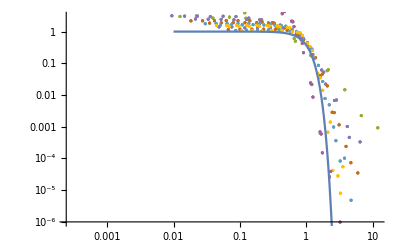

```mathematica
Module[{ plotpoints},plotpoints =Table[{((#x0)/xscale[#mu,#alpha])^(1/(1+#alpha)),Around[#hom,{#dhomLow,#dhomHigh}]/homscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha==α&&#mu<1&&#x0>0&&#hom>0&]],{α,αlist}];
Show[ListLogLogPlot[plotpoints,PlotRange->{All,{10^-6,3}},IntervalMarkersStyle->{"FenceWidth"->Thick}],
LogLogPlot[Exp[-x^3],{x,.01,100}]]]
```

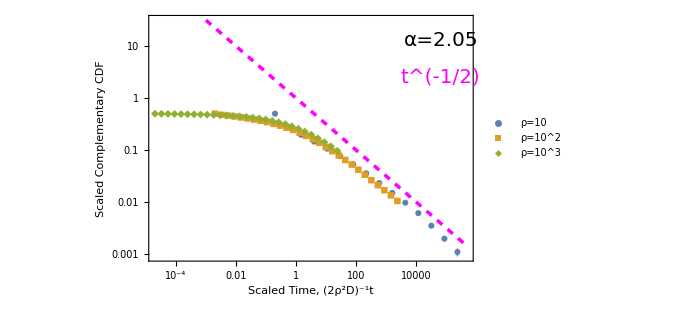

```mathematica
Module[{α=2.05, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-2)*D)^(1/(1 - 2))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow/(2*Sin[Pi/2])|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh/(2*Sin[Pi/2])|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf/(2*Sin[Pi/2])|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[x^(-1/2),{x,.001,500000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["t^(-1/2)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^2D)^-1t","Scaled Complementary CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

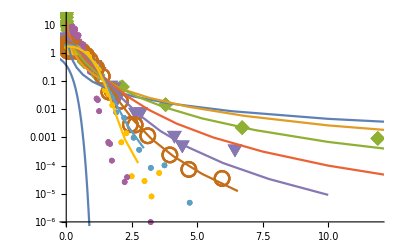

```mathematica
Module[{ plotpoints},plotpoints =Table[{((#x0)/xscale[#mu,#alpha])^(1/(1+#alpha)),Around[#hom,{#dhomLow,#dhomHigh}]/homscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha==α&&#mu<1&&#x0>0&&#hom>0&]],{α,αlist}];
Show[ListLogPlot[plotpoints,PlotRange->{All,{10^-6,20}},PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>],
ListLogPlot[Table[{x^(1/(1+α)),intvals[α][x]},{α,αlist},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True],
LogLogPlot[Exp[-x^3],{x,.01,100}]]]
```

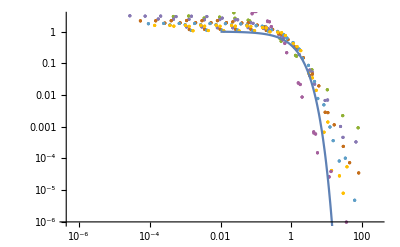

```mathematica
Module[{ plotpoints},plotpoints =Table[{((#x0)/xscale[#mu,#alpha]),Around[#hom,{#dhomLow,#dhomHigh}]/homscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha==α&& #mu<1&&#x0>0&&#hom>0&]],{α,αlist}];
Show[ListLogLogPlot[plotpoints,PlotRange->{All,{10^-6,3}}],
LogLogPlot[Exp[-x],{x,.01,100}]]]
```

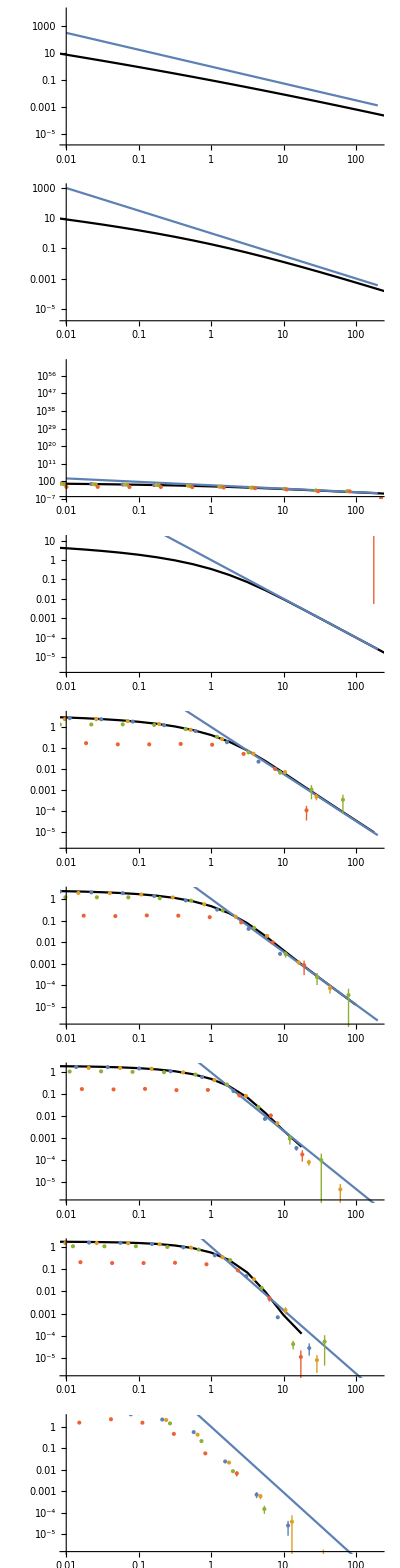

```mathematica
GraphicsColumn[Table[Module[{coal =.01, plotpoints},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/homscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&&#hom>0&]],{μ,μlist}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->Black,
PlotRange->{{.01,200},{10^-5.8,All}}],
LogLogPlot[x^(-1-α),{x,.01,200}],
ListLogLogPlot[plotpoints]]],{α,αlist}]]
```

# Math

```mathematica
Module[{alpha=1.25, coal=0.01, mu = 0.01, plotds},
LogLogPlot[fLT[x,mu,alpha]/hom[x,coal,mu,alpha],{x,1, 2 10^5}]]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

-Graphics-

```mathematica
FourierCosTransform[1/(1+k),k,x]
```

(-2 Cos[x] CosIntegral[x]+Sin[x] (π-2 SinIntegral[x]))/(√(2 π))

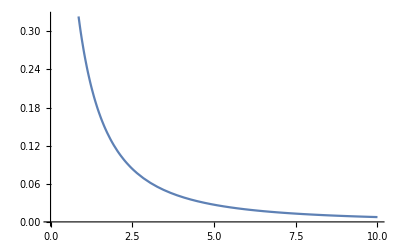

```mathematica
Plot[(-2 Cos[x] CosIntegral[x]+Sin[x] (π-2 SinIntegral[x]))/(√(2 π)),{x,0,10}]
```

```mathematica
Simplify[LaplaceTransform[Exp[-x^2/(d t)],t,μ],Assumptions->{x>0,d>0}]
```

(2 x BesselK[1,(2 x)/(√(d/μ))])/(√(d μ))

```mathematica
FourierCosTransform[1/(μ+d k^2),k,x]
```

(ⅇ^(-x/(√(d/μ))) √(π/2) √(d/μ))/d

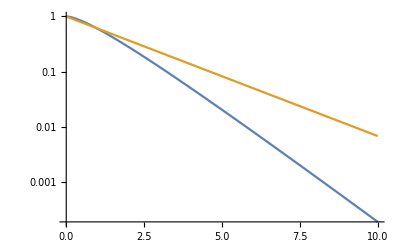

```mathematica
LogPlot[{x BesselK[1,x],Exp[-x/2]},{x,0,10}]
```

```mathematica
FourierCosTransform[Exp[-d t k^2],k,x]
```

(ⅇ^(-x^2/(4 d t)))/(√2 √(d t))

```mathematica
diffϕ[k_]:=Exp[-d t k^2]
```

```mathematica
LaplaceTransform[FourierTransform[diffϕ[k],k,x],t,μ]
```

(ⅇ^(-1/(√(d/(x^2 μ)))) √(π/2))/(√d √μ)

```mathematica
LaplaceTransform[FourierCosTransform[diffϕ[k],k,x],t,μ]
```

(ⅇ^(-1/(√(d/(x^2 μ)))) √(π/2))/(√d √μ)

```mathematica
FourierTransform[LaplaceTransform[diffϕ[k],t,μ],k,x,Assumptions->{μ>0,d>0,x>0}]
```

(ⅇ^(-x √(μ/d)) √(π/2))/(√d √μ)

```mathematica
FourierCosTransform[diffϕ[k],k,x]
```

(ⅇ^(-x^2/(4 d t)))/(√2 √(d t))

```mathematica
LaplaceTransform[(ⅇ^(-x^2/(4d t)))/(√(2d t)),t,μ,Assumptions->{x>0,d>0}]
```

(ⅇ^(-x √(μ/d)) √(π/2))/(√(d μ))

```mathematica
Integrate[1/(μ+d k^a),{k,0,∞},Assumptions->{μ>0,d>0,a>1}]
```

(d^(-1/a) π μ^(-1+1/a) Csc[π/a])/a

```mathematica
Integrate[Cos[k]/(1+ k^(3/2)),{k,0,∞}]
```

MeijerG[{{1/12,1/3,7/12},{}},{{0,1/12,1/3,1/3,7/12,2/3,5/6},{1/6,1/2}},1/46656]/(4 √3 π^(5/2))

```mathematica
Integrate[Cos[k]/(1+ k),{k,0,∞}]
```

-Cos[1] CosIntegral[1]+1/2 π Sin[1]-Sin[1] SinIntegral[1]

```mathematica
Integrate[Exp[- k^2]/(1+b k^a),{k,0,∞},Assumptions->{a>0,b>0}]
```

Integrate[(ⅇ^(-k^2))/(1+b k^a),{k,0,∞},Assumptions→{a>0,b>0}]

```mathematica
Integrate[1/((1+b k^a)(1+k^2)),{k,0,∞},Assumptions->{a>0,b>0}]
```

Integrate[1/((1+k^2) (1+b k^a)),{k,0,∞},Assumptions→{a>0,b>0}]

```mathematica
Integrate[Exp[- k^2]/k^a,{k,0,∞},Assumptions->{1>a>0}]
```

1/2 Gamma[1/2-a/2]

```mathematica
Integrate[Exp[- k^2]/(k+b),{k,0,∞},Assumptions->{b>0}]
```

1/2 ⅇ^(-b^2) (π Erfi[b]-ExpIntegralEi[b^2])

```mathematica
Integrate[Exp[- k^2]/k,{k,1,∞}]//N
```

0.109692

```mathematica
D[1/(b+μ^(1-1/a)),μ]
```

-((1-1/a) μ^(-1/a))/((b+μ^(1-1/a))^2)

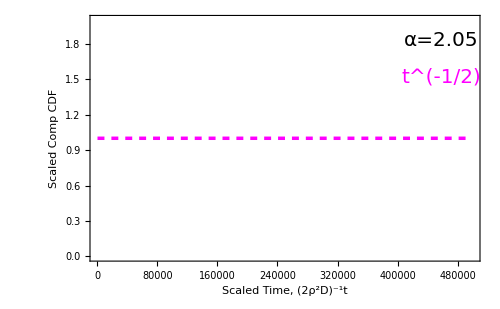

```mathematica
Show[Plot[1,{x,.001,500000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["t^(-1/2)",Magenta,20],Scaled[{.9,.75}]] },goodlabel["Scaled Time, (2ρ^2D)^-1t","Scaled Comp CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

10030.8

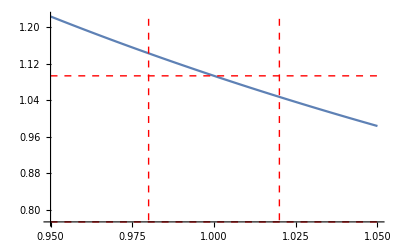

added lines Vertical

```mathematica
f[x_]:=(x^2 z)/((x^2-y^2)^2+4 q^2 x^2)/.{y->π/15,z->1,q->π/600}
Quiet[maxy=FindMaxValue[f[x],x]*1.1]
lineStyle={Thick,Red,Dashed};
lineStyle2={Thick, Black};
line1=Line[{{1+ 1/50,0},{1+1/50,maxy}}];
line2=Line[{{1-1/50,0},{1-1/50,maxy}}];
Plot[{f[x],f[1],f[1]/Sqrt[2]},{x,1-1/20,1+1/20},PlotStyle->{Automatic,Directive[lineStyle],Directive[lineStyle]},Epilog->{Directive[lineStyle],line1,line2}]

Vertical lines added
```

```mathematica
lineStyle={Thick,Black,Dashed};
```

```mathematica
lineStyle2={Thick, Black};
```

```mathematica
lineStyle3={Thick, Blue};
```

```mathematica
lineStyle4={Thick,Green};
```

```mathematica
lineStyle5={Thick,Red};
```

```mathematica
lineStyle6={Thick,Purple};
```

```mathematica
lineStyle7={Thick,Yellow};
```

```mathematica
lineStyle8={Thick,White};
```

```mathematica
line99=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line0=Line[{{0,0},{0,2}}];
```

```mathematica
line1=Line[{{1,0},{1,1}}];
```

```mathematica
line2=Line[{{2,0},{2,1}}];
```

```mathematica
line3=Line[{{3,0},{3,2}}];
```

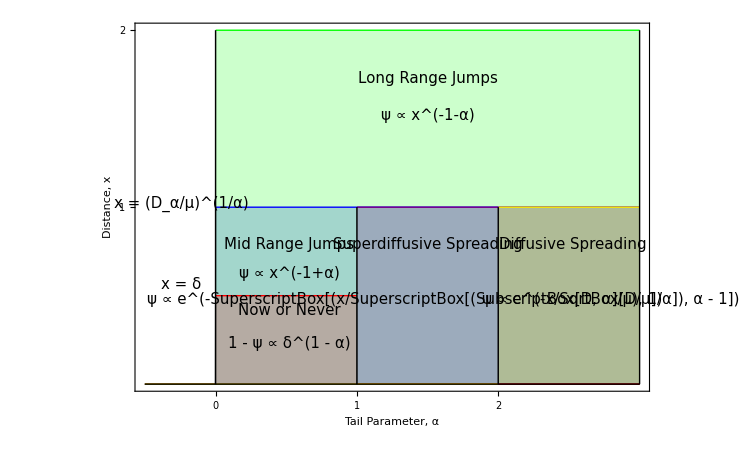

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .5*UnitStep[x] -.5*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]  },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7]},Epilog->{Directive[lineStyle2],, 
Text[Style["x = (D_α/μ)^(1/α)",Black,15],Scaled[{.09,.51}]],Text[Style["x = δ",Black,15],Scaled[{.09,.29}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.85}]],Text[Style["ψ ∝ x^(-1-α) ",Black,15],Scaled[{.57,.75}]],  Text[Style["Superdiffusive Spreading",Black,15],Scaled[{.57,.40}]],Text[Style["ψ ∝ e^(-SuperscriptBox[(x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]), α - 1]) ",Black,15],Scaled[{.6,.25}]], Text[Style["Mid Range Jumps",Black,15],Scaled[{.3,.40}]],Text[Style["ψ ∝ x^(-1+α)",Black,15],Scaled[{.30,.32}]] ,Text[Style["1 - ψ ∝ δ^(1 - α)",Black,15],Scaled[{.30,.13}]],Text[Style["Now or Never",Black,15],Scaled[{.30,.22}]] ,Text[Style[" ψ ∝ e^(-x/SqrtBox[D/μ])",Black,15],Scaled[{.85,.25}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.40}]],line0,line1, line2, line3}, ImageSize->750, Filling -> Bottom], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{{1,"Alice"},{2,"Bob"}}}},goodlabel["Tail Parameter, α","Distance, x",20], FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

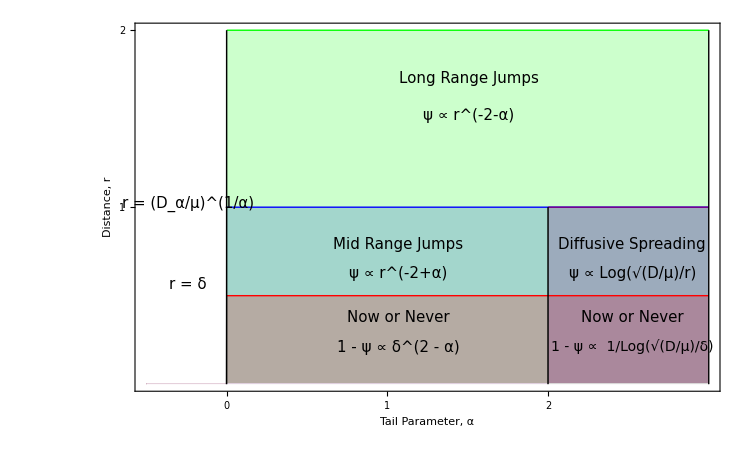

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .5*UnitStep[x], UnitStep[x -2], 0,0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["r = (D_α/μ)^(1/α)",Black,15],Scaled[{.09,.51}]],Text[Style["r = δ",Black,15],Scaled[{.09,.29}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.85}]],Text[Style["ψ ∝ r^(-2-α) ",Black,15],Scaled[{.57,.75}]],   Text[Style["Mid Range Jumps",Black,15],Scaled[{.45,.40}]],Text[Style["ψ ∝ r^(-2+α)",Black,15],Scaled[{.45,.32}]], Text[Style["1 - ψ ∝ δ^(2 - α)",Black,15],Scaled[{.45,.12}]],Text[Style[" ψ ∝ Log(√(D/μ)/r)",Black,15],Scaled[{.85,.32}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.40}]], Text[Style["Now or Never",Black,15],Scaled[{.45,.20}]],Text[Style["1 - ψ ∝  1/Log(√(D/μ)/δ)",Black,14],Scaled[{.85,.12}]],Text[Style["Now or Never",Black,15],Scaled[{.85,.20}]],line0, line2, line3}, ImageSize->750, Filling -> Bottom], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{{1,"Alice"},{2,"Bob"}}}},goodlabel["Tail Parameter, α","Distance, r",20], FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

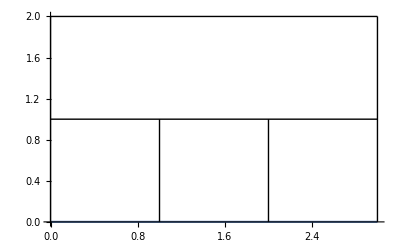

```mathematica
Plot[{0, 1,2},{x,0 ,3 },PlotStyle->{Automatic,Directive[lineStyle2],Directive[lineStyle2]},Epilog->{Directive[lineStyle2],line0,line1, line2, line3}]
```

```mathematica
Null
```

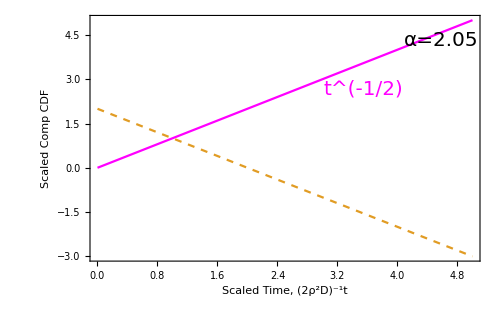

```mathematica
Show[Plot[{x, 1-(x-1)}, {x,.001,5},PlotStyle->{Magenta,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["t^(-1/2)",Magenta,20],Scaled[{.7,.7}]] },goodlabel["Scaled Time, (2ρ^2D)^-1t","Scaled Comp CDF",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

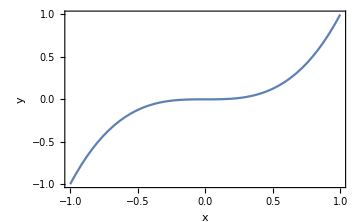

```mathematica
Show[Plot[x^3,{x,-1,1},Frame->True,ImageSize->Medium,FrameLabel->{"x","y"},PlotRange->{{-1,1},{-1,1}}],PlotRangeClipping->False,Epilog->Text[Style["A",Bold,14,Red],ImageScaled@{.05,.98}]]
```

```mathematica
line999=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line00=Line[{{0,0},{0,2}}];
```

```mathematica
line11=Line[{{1,1},{1,2}}];
```

```mathematica
line22=Line[{{2,0},{2,2}}];
```

```mathematica
line33=Line[{{3,0},{3,2}}];
```

```mathematica
line44=Line[{{0,2},{3,2}}];
```

```mathematica
line55=Line[{{0,0},{3,0}}];
```

```mathematica
line66=Line[{{0,1},{3,1}}];
```

```mathematica
line77=Line[{{0,.5},{1,.5}}];
```

```mathematica
line88=Line[{{0,.5},{3,.5}}];
```

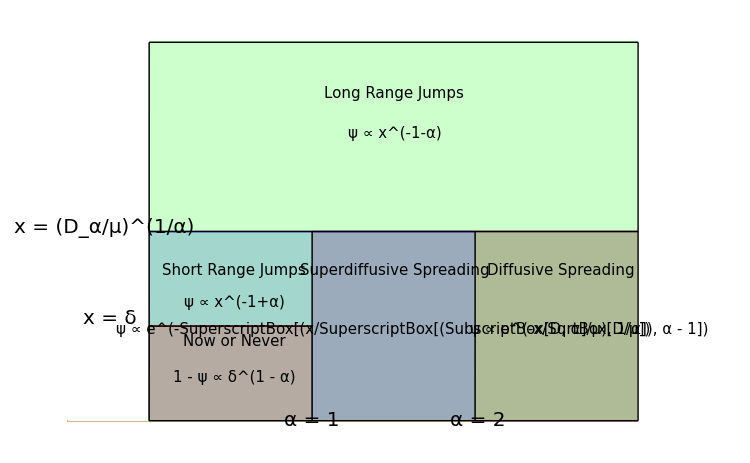

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .5*UnitStep[x] -.5*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]  },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8], Directive[lineStyle7], Directive[lineStyle7]},Epilog->{Directive[lineStyle2],Text[Style["α = 1",Black,20],Scaled[{.43,.02}]],Text[Style["α = 2",Black,20],Scaled[{.71,.02}]], 
Text[Style["x = (D_α/μ)^(1/α)",Black,20],Scaled[{.08,.51}]],Text[Style["x = δ",Black,20],Scaled[{.09,.28}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.85}]],Text[Style["ψ ∝ x^(-1-α) ",Black,15],Scaled[{.57,.75}]],  Text[Style["Superdiffusive Spreading",Black,15],Scaled[{.57,.40}]],Text[Style["ψ ∝ e^(-SuperscriptBox[(x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]), α - 1]) ",Black,15],Scaled[{.6,.25}]], Text[Style["Short Range Jumps",Black,15],Scaled[{.3,.40}]],Text[Style["ψ ∝ x^(-1+α)",Black,15],Scaled[{.30,.32}]] ,Text[Style["1 - ψ ∝ δ^(1 - α)",Black,15],Scaled[{.30,.13}]],Text[Style["Now or Never",Black,15],Scaled[{.30,.22}]] ,Text[Style[" ψ ∝ e^(-x/SqrtBox[D/μ])",Black,15],Scaled[{.85,.25}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.40}]],line00,line1, line2, line3, line55, line44, line66, line77}, ImageSize->750, Filling -> Bottom], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{}}},Frame->False, Axes -> False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

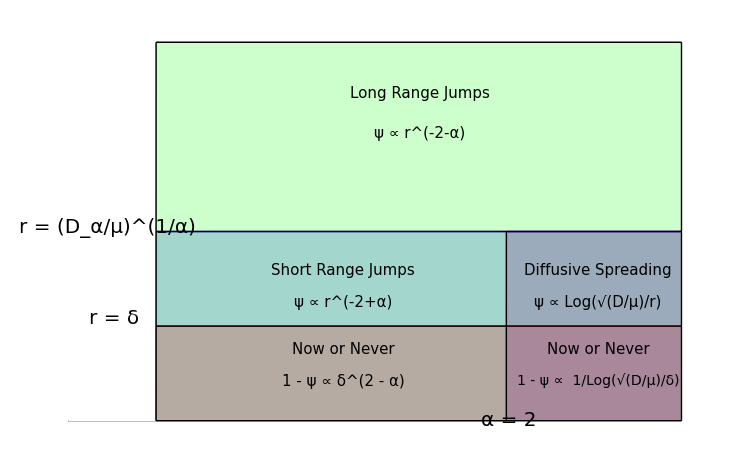

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .5*UnitStep[x], UnitStep[x -2], 0,0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2],Text[Style["α = 2",Black,20],Scaled[{.71,.02}]], 
Text[Style["r = (D_α/μ)^(1/α)",Black,20],Scaled[{.08,.51}]],Text[Style["r = δ",Black,20],Scaled[{.09,.28}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.85}]],Text[Style["ψ ∝ r^(-2-α) ",Black,15],Scaled[{.57,.75}]],   Text[Style["Short Range Jumps",Black,15],Scaled[{.45,.40}]],Text[Style["ψ ∝ r^(-2+α)",Black,15],Scaled[{.45,.32}]], Text[Style["1 - ψ ∝ δ^(2 - α)",Black,15],Scaled[{.45,.12}]],Text[Style[" ψ ∝ Log(√(D/μ)/r)",Black,15],Scaled[{.85,.32}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.40}]], Text[Style["Now or Never",Black,15],Scaled[{.45,.20}]],Text[Style["1 - ψ ∝  1/Log(√(D/μ)/δ)",Black,14],Scaled[{.85,.12}]],Text[Style["Now or Never",Black,15],Scaled[{.85,.20}]],line0, line2, line3, line44, line55, line66, line88}, ImageSize->750, Filling -> Bottom], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{}}},Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

```mathematica
line999=Line[{{-.5,0},{-.5,-2}}];
```

```mathematica
line00=Line[{{0,0},{0,-2}}];
```

```mathematica
line11=Line[{{1,0},{1,-1}}];
```

```mathematica
line22=Line[{{2,0},{2,-1}}];
```

```mathematica
line33=Line[{{3,0},{3,-2}}];
```

```mathematica
line44=Line[{{0,-2},{3,-2}}];
```

```mathematica
line55=Line[{{0,0},{3,0}}];
```

```mathematica
line66=Line[{{0,-1},{3,-1}}];
```

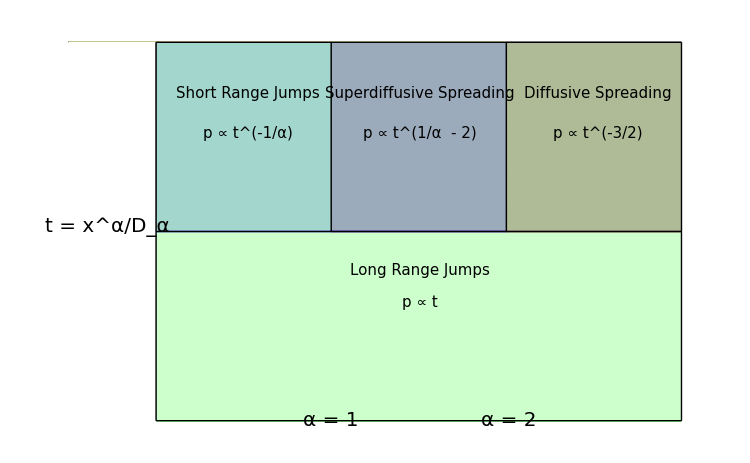

```mathematica
Show[Plot[{0,- UnitStep[x] ,-2*UnitStep[x] ,  -UnitStep[x -1] + UnitStep[x -4],  -UnitStep[x -2],-UnitStep[x -3]  },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle6],  Directive[lineStyle7], Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["α = 1",Black,20],Scaled[{.43,.02}]],Text[Style["α = 2",Black,20],Scaled[{.71,.02}]], 
Text[Style["t = x^α/D_α",Black,20],Scaled[{.08,.51}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.40}]],Text[Style["p ∝ t^(1/α  - 2) ",Black,15],Scaled[{.57,.75}]],Text[Style["p ∝ t ",Black,15],Scaled[{.57,.32}]],  Text[Style["Superdiffusive Spreading",Black,15],Scaled[{.57,.85}]],Text[Style["p ∝ t^(-1/α) ",Black,15],Scaled[{.3,.75}]], Text[Style["Short Range Jumps",Black,15],Scaled[{.3,.85}]],Text[Style[" p ∝ t^(-3/2)",Black,15],Scaled[{.85,.75}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.85}]],line00,line11, line22, line33, line44, line55, line66}, ImageSize->750, Filling ->Top], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{}}},Frame->False, Axes -> False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

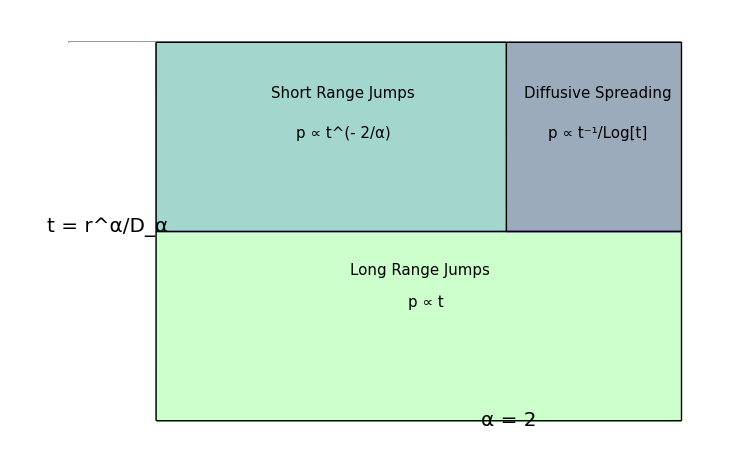

```mathematica
Show[Plot[{0, -UnitStep[x],-2*UnitStep[x]+2*UnitStep[x-3], -UnitStep[x -2], 0   },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle6],Directive[lineStyle8]  },Epilog->{Directive[lineStyle2],Text[Style["α = 2",Black,20],Scaled[{.71,.02}]], 
Text[Style["t = r^α/D_α",Black,20],Scaled[{.08,.51}]], Text[Style["Long Range Jumps",Black,15],Scaled[{.57,.40}]],Text[Style["p ∝ t^(- 2/α) ",Black,15],Scaled[{.45,.75}]],   Text[Style["Short Range Jumps",Black,15],Scaled[{.45,.85}]],Text[Style["p ∝ t",Black,15],Scaled[{.58,.32}]], Text[Style[" p ∝ t^-1/Log[t]",Black,15],Scaled[{.85,.75}]], Text[Style["Diffusive Spreading",Black,15],Scaled[{.85,.85}]],line00, line22, line33, line44, line55, line66, line88}, ImageSize->750, Filling -> Top], FrameTicks->{{{1,2,3},None},{{{1,1},{2,2}, {0,0}},{}}},Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```